```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Google class function 4 variant
```

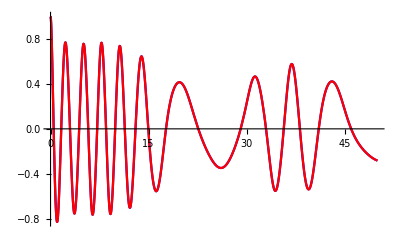

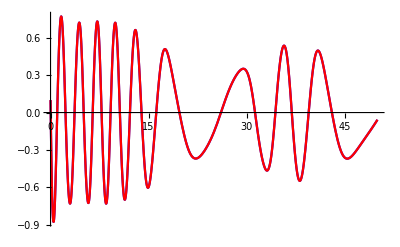

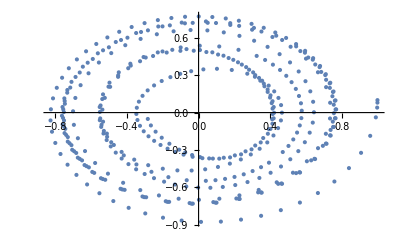

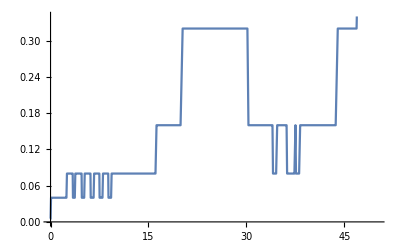

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1, H]
A = 0.0;
B=50.0;
H = (x1[t]^2+x2[t]^2)^2-0.02(x1[t]^2-x2[t]^2);
s1 = NDSolve[{x1'[t]==D[H,x2[t]]-0.1*H*D[H,x1[t]]+0.15*x2[t]*Sin[0.25*t],x2'[t]==-D[H,x1[t]]-0.1*H*D[H,x2[t]]+0.15*x2[t]*Sin[0.25*t], x1[0.0]==1.0,x2[0.0]==0.1},{x1[t],x2[t]},{t, A,B}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
tau = Flatten[Import["tau.txt","Data"]];
stepTau =  DeleteDuplicates[Table[{tf[[i]], tau[[i]]},{i,1,Length[tf]}]];
t0 = DeleteDuplicates[Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}]];
t1 = DeleteDuplicates[Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}]];
faseportrait =  DeleteDuplicates[Table[{res0[[i]], res1[[i]]},{i,1,Length[res0]}]];
g0 = Plot[Interpolation[t0][x],{x,A,B},PlotStyle->Blue];
g1 = Plot[Interpolation[t1][x],{x,A,B},PlotStyle->Blue];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,A,B},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,A,B},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
ListPlot[faseportrait]
ListLinePlot[stepTau]
```

```mathematica
Toolkit function from pendulum
```

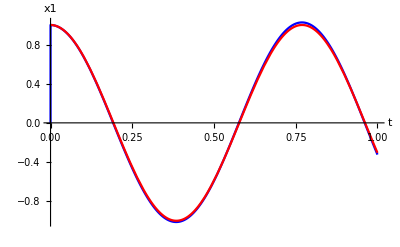

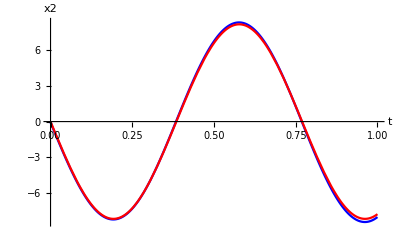

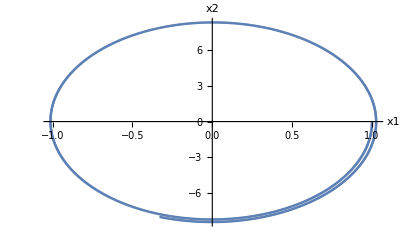

```mathematica
Clear[s1,tf,res0,res1,t0,t1,g0,g1,ge0,ge1, H,k,m, tau, stepTau]
A = 0.0;k=20.0;
B=1.0;m = 0.3;
s1 = NDSolve[{x1'[t]==x2[t],x2'[t]==-k/m x1[t], x1[0.0]==1.0,x2[0.0]==0.0},{x1[t],x2[t]},{t, A,B}];
tf = Flatten[Import["t.txt","Data"]];
res0 = Flatten[Import["res0.txt","Data"]];
res1 = Flatten[Import["res1.txt","Data"]];
t0 = DeleteDuplicates[Table[{tf[[i]], res0[[i]]},{i,1,Length[tf]}]];
t1 = DeleteDuplicates[Table[{tf[[i]], res1[[i]]},{i,1,Length[tf]}]];
(*tau = Flatten[Import["tau.txt","Data"]];
stepTau =  DeleteDuplicates[Table[{tf[[i]], tau[[i]]},{i,1,Length[tf]}]];*)
faseportrait =  DeleteDuplicates[Table[{res0[[i]], res1[[i]]},{i,1,Length[res0]}]];
g0 = ListLinePlot[t0,PlotStyle->Blue,AxesLabel->{"t","x1"}];
g1 = ListLinePlot[t1,PlotStyle->Blue,AxesLabel->{"t","x2"}];
ge0 = Plot[Evaluate[x1[t]/.s1],{t,A,B},PlotStyle->Red];
ge1 = Plot[Evaluate[x2[t]/.s1],{t,A,B},PlotStyle->Red];
Show[g0,ge0, PlotRange->All]
Show[g1,ge1, PlotRange->All]
ListPlot[faseportrait,AxesLabel->{"x1","x2"}]
(*ListLinePlot[stepTau,AxesLabel->{"t","τ"}]*)
```